```mathematica
Clear["Global`*"];
SetDirectory@NotebookDirectory[];
```

## Reallocating the House of Representatives

The functions for applying an apportionment algorithm are all contained here

```mathematica
Get["https://www.wolframcloud.com/objects/d9d85855-d591-49b8-bbd0-ecb7700cc503"]
```

Syntax::sntx: Invalid syntax in or before "
      <!DOCTYPE html PUBLIC "-//W3C//DTD XHTML 1.0 Transitional//EN" "http://www.w3.org/TR/xhtml1/DTD/xhtml1-transitional.dtd">"
       ^
     (line 1 of "https://www.wolframcloud.com/objects/d9d85855-d591-49b8-bbd0-ecb7700cc503").

Let’s start with no modified parameters

```mathematica
plainResults = calculateAllocations[]
```

<|AK→1,AL→7,AR→4,AZ→9,CA→53,CO→7,CT→5,DE→1,FL→27,GA→14,HI→2,IA→4,ID→2,IL→18,IN→9,KS→4,KY→6,LA→6,MA→9,MD→8,ME→2,MI→14,MN→8,MO→8,MS→4,MT→1,NC→13,ND→1,NE→3,NH→2,NJ→12,NM→3,NV→4,NY→27,OH→16,OK→5,OR→5,PA→18,RI→2,SC→7,SD→1,TN→9,TX→36,UT→4,VA→11,VT→1,WA→10,WI→8,WV→3,WY→1|>

And compare it to the current allocation

```mathematica
compareAllocations[plainResults]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID
actual reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
calculated reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
calculated reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI
actual reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
calculated reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
state | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
calculated reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

Now let’s see what happens if we increase the size of the House to 2,000 members instead of 435!

```mathematica
bigHouse = calculateAllocations[2000];
compareAllocations[bigHouse]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID
actual reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
calculated reps | 5 | 31 | 19 | 41 | 242 | 33 | 23 | 6 | 122 | 63 | 9 | 20 | 10
difference | 4 | 24 | 15 | 32 | 189 | 26 | 18 | 5 | 95 | 49 | 7 | 16 | 8
state | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
calculated reps | 83 | 42 | 19 | 28 | 29 | 43 | 37 | 9 | 64 | 34 | 39 | 19 | 6
difference | 65 | 33 | 15 | 22 | 23 | 34 | 29 | 7 | 50 | 26 | 31 | 15 | 5
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI
actual reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
calculated reps | 62 | 4 | 12 | 9 | 57 | 13 | 18 | 126 | 75 | 24 | 25 | 82 | 7
difference | 49 | 3 | 9 | 7 | 45 | 10 | 14 | 99 | 59 | 19 | 20 | 64 | 5
state | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
calculated reps | 30 | 5 | 41 | 163 | 18 | 52 | 4 | 44 | 37 | 12 | 4 | 2000
difference | 23 | 4 | 32 | 127 | 14 | 41 | 3 | 34 | 29 | 9 | 3 | 1565

That' s all interesting, but did it succeed in evening out the ratio of people per representative?

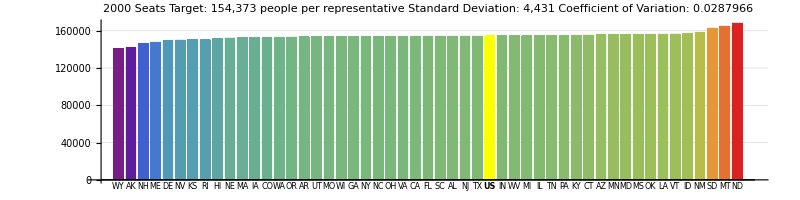

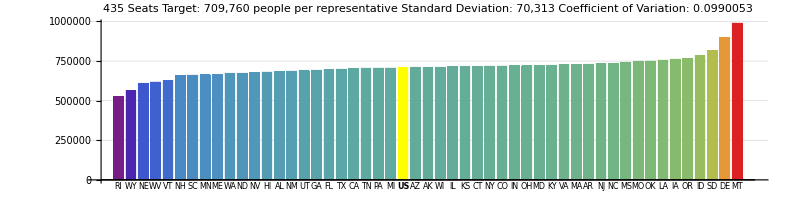

```mathematica
visualizeRatio[bigHouse]
visualizeRatio[houseOfRepresentatives]
```

It did! But what we’re equally interested in different algorithms than Huntington-Hill for divvying up the representatives.

Just to remind ourselves, seats are allotted one-by-one based on priority. A priority function takes a given state’s two-letter name and the number of seats currently allocated to that state, and spits out a number. Whichever of the 50 states has the highest number gets the next seat. The current method is the Huntington-Hill method:

P/(√(n (1+n)))

priorityHuntingtonHill[stateAbbr_, stateEVs_] := 
	1.0 * statesByAbbreviation[stateAbbr][“population_decennial”][“2010”] / 	Sqrt[stateEVs * (stateEVs + 1)]

Recall that `caclulateAllocations` can take any priority function, in addition to the minimum that each state gets, which shouldn’t be lower than one.

calculateAllocations[total_:435, min_:1, priorityFunc_:priorityHuntingtonHill] := (...)

Let' s start with a fairly basic priority function that simply allots the next seat to the state with the highest peoplePerRep ratio with 435 seats.

```mathematica
priorityEqualRatios[stateAbbr_, stateEVs_] :=
	1.0 * statesByAbbreviation[stateAbbr]["population_decennial"]["2010"] / stateEVs
```

```mathematica
equalRatios = calculateAllocations[435, 1, priorityEqualRatios];
```

```mathematica
compareAllocations[equalRatios]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID
actual reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
calculated reps | 1 | 7 | 4 | 9 | 50 | 7 | 5 | 2 | 26 | 13 | 2 | 5 | 3
difference | 0 | 0 | 0 | 0 | -3 | 0 | 0 | 1 | -1 | -1 | 0 | 1 | 1
state | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
calculated reps | 18 | 9 | 4 | 6 | 7 | 9 | 8 | 2 | 14 | 8 | 9 | 4 | 2
difference | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI
actual reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
calculated reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 26 | 16 | 6 | 6 | 18 | 2
difference | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 1 | 1 | 0 | 0
state | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
calculated reps | 7 | 2 | 9 | 34 | 4 | 11 | 1 | 9 | 8 | 3 | 1 | 435
difference | 0 | 1 | 0 | -2 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0

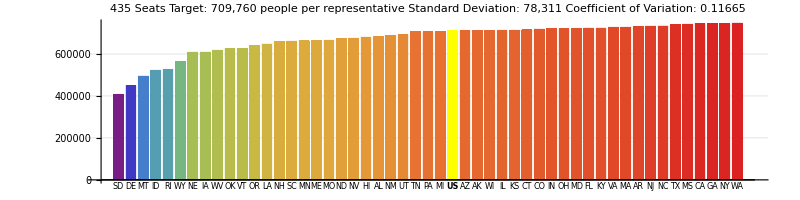

```mathematica
visualizeRatio[equalRatios]
```

So that method didn’t go so well. In fact, it did worse than the current method. Let’s try it with more seats.

```mathematica
Manipulate[
	visualizeRatio@calculateAllocations[t, 1, priorityEqualRatios], {{t, 435, "Total Seats"}, 50, 3000, 10},
	Alignment->Center, LabelStyle->{Large, Red}, ControlPlacement->Top
]
```

```mathematica
countEVs = calculateAllocations[635, 5];
countEVs = countEVs - 4;
```

```mathematica
compareAllocations[countEVs]
```

state | AK | AL | AR | AZ | CA | CO | CT | DE | FL | GA | HI | IA | ID
actual reps | 1 | 7 | 4 | 9 | 53 | 7 | 5 | 1 | 27 | 14 | 2 | 4 | 2
calculated reps | 1 | 5 | 2 | 8 | 66 | 5 | 3 | 2 | 31 | 14 | 2 | 2 | 2
difference | 0 | -2 | -2 | -1 | 13 | -2 | -2 | 1 | 4 | 0 | 0 | -2 | 0
state | IL | IN | KS | KY | LA | MA | MD | ME | MI | MN | MO | MS | MT
actual reps | 18 | 9 | 4 | 6 | 6 | 9 | 8 | 2 | 14 | 8 | 8 | 4 | 1
calculated reps | 20 | 8 | 2 | 4 | 5 | 8 | 7 | 2 | 15 | 6 | 7 | 2 | 2
difference | 2 | -1 | -2 | -2 | -1 | -1 | -1 | 0 | 1 | -2 | -1 | -2 | 1
state | NC | ND | NE | NH | NJ | NM | NV | NY | OH | OK | OR | PA | RI
actual reps | 13 | 1 | 3 | 2 | 12 | 3 | 4 | 27 | 16 | 5 | 5 | 18 | 2
calculated reps | 14 | 1 | 2 | 2 | 12 | 2 | 2 | 32 | 18 | 3 | 3 | 20 | 2
difference | 1 | 0 | -1 | 0 | 0 | -1 | -2 | 5 | 2 | -2 | -2 | 2 | 0
state | SC | SD | TN | TX | UT | VA | VT | WA | WI | WV | WY | Total
actual reps | 7 | 1 | 9 | 36 | 4 | 11 | 1 | 10 | 8 | 3 | 1 | 435
calculated reps | 5 | 2 | 8 | 43 | 2 | 11 | 1 | 9 | 7 | 2 | 1 | 435
difference | -2 | 1 | -1 | 7 | -2 | 0 | 0 | -1 | -1 | -1 | 0 | 0

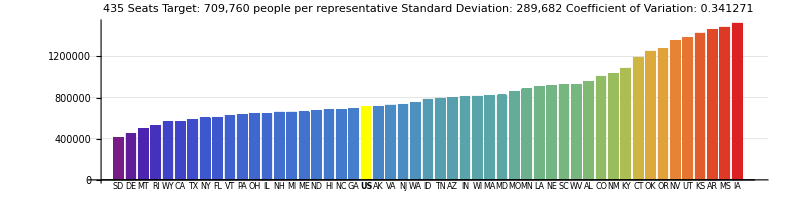

```mathematica
visualizeRatio[countEVs]
```